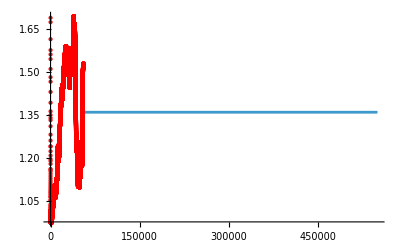

```mathematica
(*============================================================*)
(*1. SETUP:Data Loading and Function Definitions*)
(* ===================================================================*)
(* Read atmospheric 14C data*)
SetDirectory["/Users/flamholz/Documents/workspace/soil_diskin/notebooks"];
C14DATADIR="../data/14C_atm_annot.csv";
C14DATA=Import[C14DATADIR, "HeaderLines"-> 1];
C14DATA= C14DATA[[All,{4,5}]];
(*Interpolate the 14C data, use the mean ratio for extrapolation*)
MeanR = Last[Mean[C14DATA[[-50000;;]]]];
atm14C=Interpolation[C14DATA,InterpolationOrder->0,"ExtrapolationHandler"-> {(MeanR&)}];

(* Plot the results of the interpolation to see it makes sense *)
Plot[atm14C[x],{x,0,550000},Epilog->{PointSize[Medium],Red,Point[C14DATA]}]
```

```mathematica
(* Define the function that calculates the radiocarbon signal from the inputs of the turnover time and mean age of the system *)
LognormalRadiocarbon[tau_,age_] := (
sig = Sqrt[Log[age/tau]];
mu = -Log[Sqrt[tau^3/age]];
r = NIntegrate[ atm14C[a]*Exp[-a/8267]* PDF[LogNormalDistribution[mu,sig],x] * Exp[-x*a] / Exp[-mu+(sig^2)/2],{x,0,Infinity},{a,0,Infinity}, PrecisionGoal->3];
r
)

(* Define the function that optimizes the mean age for a given turnover time and observed radiocarbon signal *)
FindOptimalAge[tau_?NumericQ,rtrue_?NumericQ,InitialAge_?NumericQ]:=(
Module[{objectiveFunction,solution},
(*Define the objective function to minimize:the squared difference between the function output and r_true*)
objectiveFunction[age_?NumericQ]:=(LognormalRadiocarbon[tau,age]-rtrue)^2;
(*Use FindMinimum to find the age that minimizes the objective function*)
(*FindMinimum requires a starting point for'age'*)
solution=Quiet[FindMinimum[objectiveFunction[age],{age,InitialAge}, AccuracyGoal->8, MaxIterations->100]];
(*solution=FindMinimum[objectiveFunction[age],{age,InitialAge}, AccuracyGoal->8, MaxIterations->100];*)
(*Return the value of age that minimizes the difference*)
Return[age/. Last[solution]]]
)
```

```mathematica
LaunchKernels[];

(*3. Distribute definitions to parallel kernels*)
(*Make sure all symbols that FindOptimalAge and LognormalRadiocarbon depend on are distributed.*)
(*atm14C is already defined globally.If it were a more complex structure or function,you'd want to be sure it's available.*)
DistributeDefinitions[LognormalRadiocarbon,FindOptimalAge,atm14C];

agelist = 10^Range[3,5.5, (5.5-3)/100];
ScanAges[tau_] := Module[{ages}, ages =Table[Quiet[LognormalRadiocarbon[tau, i]],{i,agelist}];
Return[ages]]
```

```mathematica
results=ParallelMap[ScanAges[#]&,data[[All,1]]]
Export["../results/03b_lognormal_model_age_scan.csv",results,"CSV"]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

{}

../results/03b_lognormal_model_age_scan.csv

ScanAges